## Routing a robot to collect data from n underwater sensors in mimum time we were transmitting only whle paused Srikanth K.V.S. and Aaron T. Becker

### Set up a simulation

### Models for communication. We have a Magnetic induction transmitter and an Acoutic transmitter The models below are made up. Miao Pan has data. I want bits per second as a function of distance

```mathematica
bitsPerSecMagneticInduc[dist_]:= 20 ⅇ^(-dist/10)
bitsPerSecAccoustic[dist_]:= 2 ⅇ^(-dist/100)
```

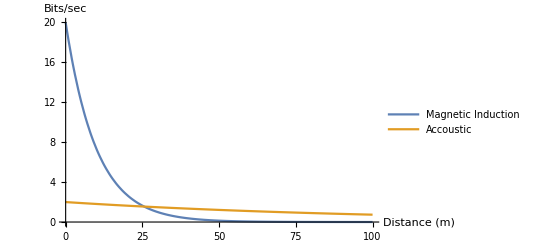

```mathematica
Plot[{bitsPerSecMagneticInduc[dist],bitsPerSecAccoustic[dist]},{dist,0,100},PlotRange->All,AxesLabel->{"Distance (m)","Bits/sec"},PlotLegends->{"Magnetic Induction","Accoustic"}]
```

### Example Calculations

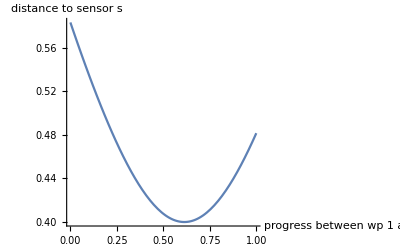

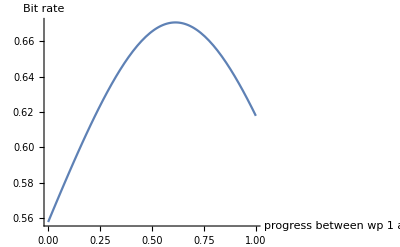

(0.694135 ∫_0^1 ⅇ^(-√((-0.132409-0.348019 t) (-0.132409-0.348019 Conjugate[t])+(-0.568427+0.600588 t) (-0.568427+0.600588 Conjugate[t])))ⅆt)/v

```mathematica
p1 =RandomReal[1,{1,2}];
p2 =RandomReal[1,{1,2}];
s = RandomReal[1,{1,2}];
Plot[EuclideanDistance[p1 + (p2-p1) p, s],{p,0,1},AxesLabel->{"progress between wp 1 and 2","distance to sensor s"}]
Plot[ ⅇ^(-EuclideanDistance[p1 + (p2-p1) t, s]),{t,0,1},AxesLabel->{"progress between wp 1 and 2","Bit rate"}]
(*bits transmitted are at velocity v is: *)
EuclideanDistance[p1 ,p2]/v∫_0^1 ⅇ^(-EuclideanDistance[p1 + (p2-p1) t, s])ⅆt
```

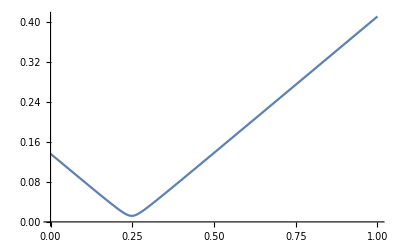
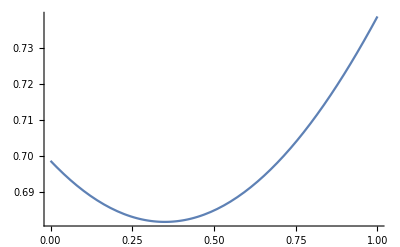
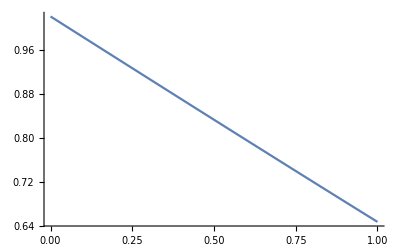

```mathematica
EuclideanDistance[p1 ,p2]/v∫_0^1 ⅇ^(-EuclideanDistance[p1 + (p2-p1) p, s])ⅆp

(√((p1x-p2x)^2+(p1y-p2y)^2))/v∫_0^1 ⅇ^(-√((p1x+(p2x-p1x)p-sx)^2+(p1y+(p2y-p1y)p-sy)^2))ⅆp
```

```mathematica
∫_0^1 ⅇ^(-√((p1x+(p2x-p1x)p-sx)^2+(p1y+(p2y-p1y)p-sy)^2))ⅆp
```

∫_0^1 ⅇ^(-√((p1x+p (-p1x+p2x)-sx)^2+(p1y+p (-p1y+p2y)-sy)^2))ⅆp

```mathematica
∫_0^1 E^(-√((p1x+(p2x-p1x)p-sx)^2+(p1y+(p2y-p1y)p-sy)^2))ⅆp
```

## (*You can put this into matlab*)

```mathematica
(Sqrt[(p1x - p2x)^2 + (p1y - p2y)^2]/v)*Integrate[E^(-Sqrt[(p1x + (p2x - p1x)*p - sx)^2 + (p1y + (p2y - p1y)*p - sy)^2]), {p, 0, 1}]
```

Gradient Descent

```mathematica
D[√((xr-xrp1)^2+(yr-yrp1)^2)+√((xr-xrm1)^2+(yr-yrm1)^2),xr]
D[√((xr-xrp1)^2+(yr-yrp1)^2)+√((xr-xrm1)^2+(yr-yrm1)^2),yr]
```

(xr-xrm1)/(√((xr-xrm1)^2+(yr-yrm1)^2))+(xr-xrp1)/(√((xr-xrp1)^2+(yr-yrp1)^2))

(yr-yrm1)/(√((xr-xrm1)^2+(yr-yrm1)^2))+(yr-yrp1)/(√((xr-xrp1)^2+(yr-yrp1)^2))